## New NN test, Train/Dev/Test Split

```mathematica
ABMInputsV2=Import["/Users/thorsilver/Downloads/SocialCareOptimisation/ABM-for-social-care/lptau10round2_GEMSA_inputs.csv"];

ABMOutputsV2=Import["/Users/thorsilver/Downloads/SocialCareOptimisation/ABM-for-social-care/lptau10round2 GEMSA outputs.csv"];ABMOutputsV2=Function[x,x/1000]/@ABMOutputsV2; 
ABMAssocV2 = AssociationThread[ABMInputsV2 -> Flatten[ABMOutputsV2]];
ABMnewDataV2=Dataset[ABMAssocV2];
ABMNormalV2=Normal[ABMAssocV2];
ABMNormalRandom=RandomSample[ABMNormalV2];
ABMtrainv2=TakeDrop[ABMNormalV2,320];
ABMtestv2=ABMtrainv2[[2]];
ABMtraining=ABMtrainv2[[1]];
trainDevSplit=TakeDrop[ABMtraining,256];
finalTrain=trainDevSplit[[1]];
finalDev=trainDevSplit[[2]];
finaltest=ABMtestv2;
```

```mathematica
Length[finalTrain]
Length[finalDev]
Length[finaltest]
```

256

64

80

```mathematica
pRFv2=Predict[finalTrain,Method->"RandomForest"]
```

PredictorFunction[…]

PredictorMeasurementsObject[…]

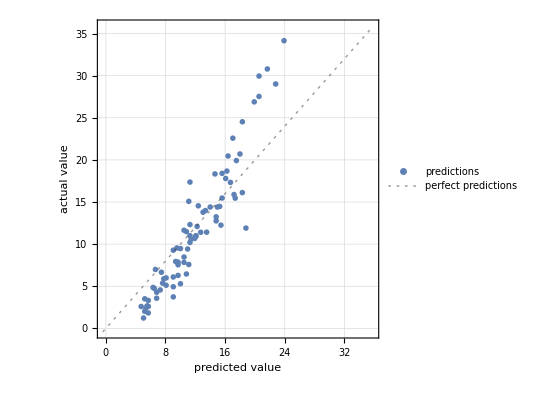

12.0599

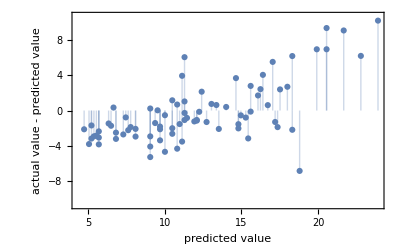

Predictor information
Data type | Mixed (number: 10)
Standard deviation | 4.27 ± 0.46
Method | RandomForest
Single evaluation time | 4.33 ms/example
Batch evaluation speed | 52. examples/ms
Loss | 2.88 ± 0.092
Model memory | 238. kB
Training examples used | 256 examples
Training time | 397. ms
 |

```mathematica
pmRFv2=PredictorMeasurements[pRFv2,finaltest]
pmRFv2["ComparisonPlot"]
pmRFv2["MeanSquare"]
pmRFv2["ResidualPlot"]
Information[pRFv2]
```

```mathematica
pXGTv2= Predict[finalTrain,Method->"GradientBoostedTrees"]
```

PredictorFunction[…]

PredictorMeasurementsObject[…]

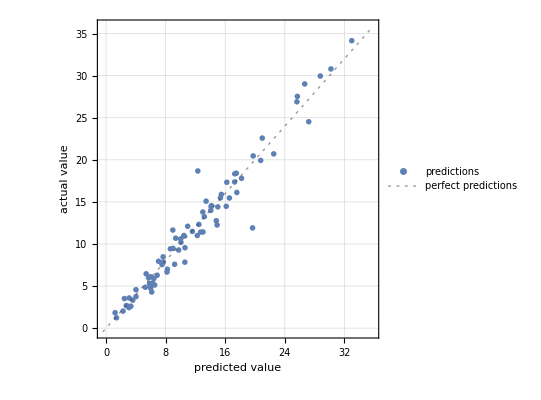

2.52565

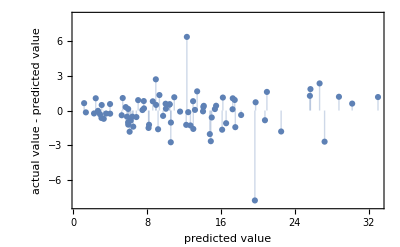

Predictor information
Data type | Mixed (number: 10)
Standard deviation | 2.41 ± 0.83
Method | GradientBoostedTrees
Single evaluation time | 3.8 ms/example
Batch evaluation speed | 43.8 examples/ms
Loss | 3.77 ± 1.
Model memory | 391. kB
Training examples used | 256 examples
Training time | 1.47 s
 |

```mathematica
pmXGTv2=PredictorMeasurements[pXGTv2,finaltest]
pmXGTv2["ComparisonPlot"]
pmXGTv2["MeanSquare"]
pmXGTv2["ResidualPlot"]
Information[pXGTv2]
```

```mathematica
pNNv2= Predict[finalTrain,Method->{"NeuralNetwork", "NetworkDepth"->3,"NetworkType"->"FullyConnected", "L2Regularization"->0.05, MaxTrainingRounds->16000}]
```

PredictorFunction[…]

PredictorMeasurementsObject[…]

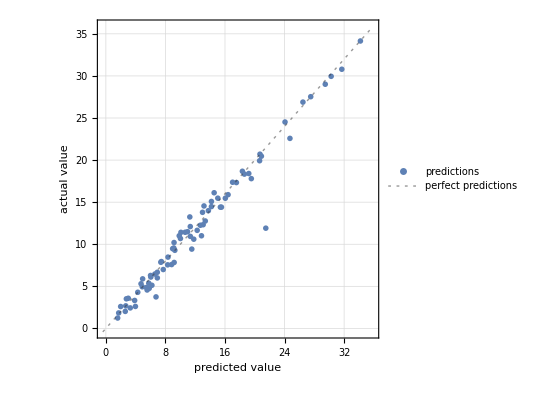

1.96365

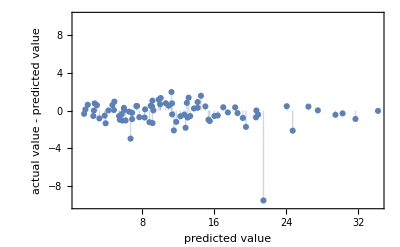

Predictor information
Data type | Mixed (number: 10)
Standard deviation | 2.18 ± 0.92
Method | NeuralNetwork
Single evaluation time | 2.16 ms/example
Batch evaluation speed | 46.7 examples/ms
Loss | 1.87 ± 0.22
Model memory | 246. kB
Training examples used | 256 examples
Training time | 1 23
 |

```mathematica
pmNNv2=PredictorMeasurements[pNNv2,finaltest]
pmNNv2["ComparisonPlot"]
pmNNv2["MeanSquare"]
pmNNv2["ResidualPlot"]
Information[pNNv2]
```

PredictorFunction[…]

PredictorMeasurementsObject[…]

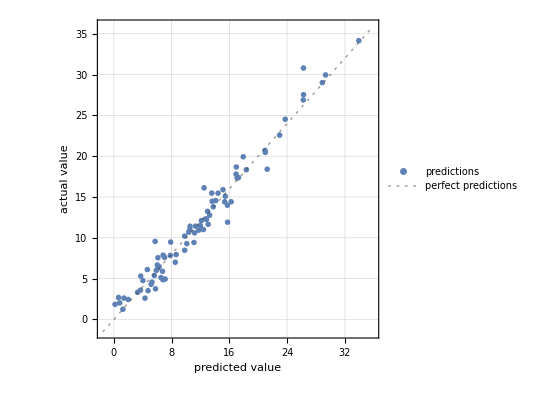

1.92845

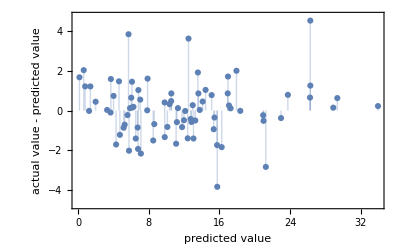

Predictor information
Data type | Mixed (number: 10)
Standard deviation | 2.19 ± 0.33
Method | GaussianProcess
Single evaluation time | 3.95 ms/example
Batch evaluation speed | 25.7 examples/ms
Loss | 1.97 ± 0.12
Model memory | 548. kB
Training examples used | 256 examples
Training time | 2.97 s
 |

```mathematica
pGPEv2=Predict[finalTrain,Method->"GaussianProcess"]
pmGPEv2=PredictorMeasurements[pGPEv2,finaltest]
pmGPEv2["ComparisonPlot"]
pmGPEv2["MeanSquare"]
pmGPEv2["ResidualPlot"]
Information[pGPEv2]
```

```mathematica
pNNv3= Predict[finalTrain,Method->{"NeuralNetwork", "NetworkDepth"->3,"NetworkType"->"FullyConnected", "L2Regularization"->0.05, MaxTrainingRounds->24000}]
pmNNv3=PredictorMeasurements[pNNv3,finaltest]
pmNNv3["ComparisonPlot"]
pmNNv3["MeanSquare"]
pmNNv3["ResidualPlot"]
Information[pNNv3]
```

PredictorFunction[…]

PredictorMeasurementsObject[…]

-Graphics-

1.96365

-Graphics-

Predictor information
Data type | Mixed (number: 10)
Standard deviation | 2.18 ± 0.92
Method | NeuralNetwork
Single evaluation time | 2.31 ms/example
Batch evaluation speed | 45.4 examples/ms
Loss | 1.87 ± 0.22
Model memory | 246. kB
Training examples used | 256 examples
Training time | 2 8
 |

PredictorFunction[…]

PredictorMeasurementsObject[…]

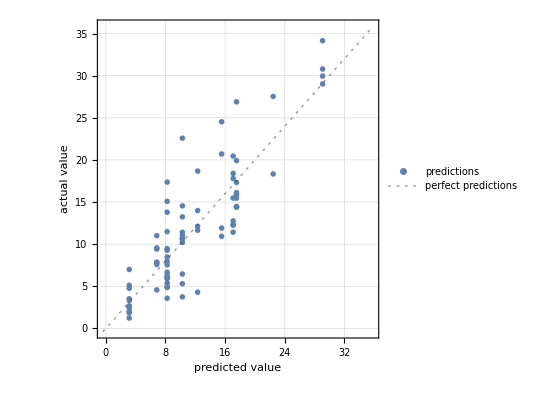

14.3214

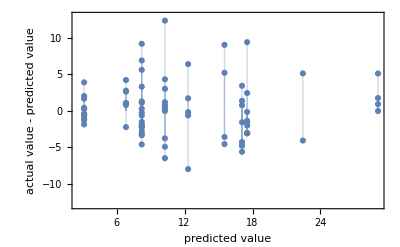

Predictor information
Data type | Mixed (number: 10)
Standard deviation | 4.99 ± 0.37
Method | DecisionTree
Single evaluation time | 1.32 ms/example
Batch evaluation speed | 305. examples/ms
Loss | 3.01 ± 0.13
Model memory | 147. kB
Training examples used | 256 examples
Training time | 355. ms
 |

```mathematica
pDTv2=Predict[finalTrain,Method->"DecisionTree"]
pmDTv2=PredictorMeasurements[pDTv2,finaltest]
pmDTv2["ComparisonPlot"]
pmDTv2["MeanSquare"]
pmDTv2["ResidualPlot"]
Information[pDTv2]
```

PredictorFunction[…]

PredictorMeasurementsObject[…]

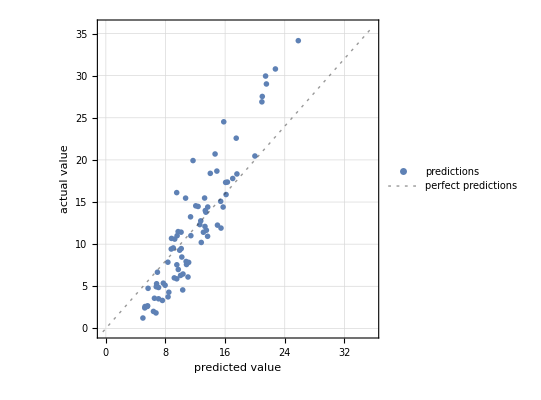

13.4224

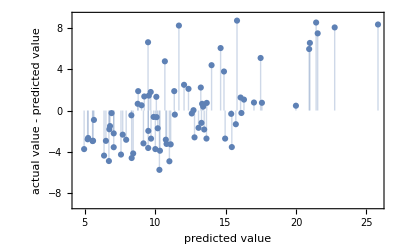

Predictor information
Data type | Mixed (number: 10)
Standard deviation | 4.84 ± 0.39
Method | NearestNeighbors
Single evaluation time | 1.28 ms/example
Batch evaluation speed | 86.2 examples/ms
Loss | 3.02 ± 0.045
Model memory | 171. kB
Training examples used | 256 examples
Training time | 350. ms
 |

```mathematica
pNearestv2=Predict[finalTrain,Method->"NearestNeighbors"]
pmNearestv2=PredictorMeasurements[pNearestv2,finaltest]
pmNearestv2["ComparisonPlot"]
pmNearestv2["MeanSquare"]
pmNearestv2["ResidualPlot"]
Information[pNearestv2]
```

PredictorFunction[…]

PredictorMeasurementsObject[…]

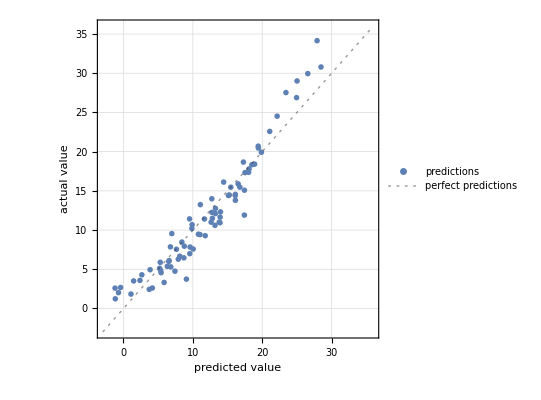

4.374

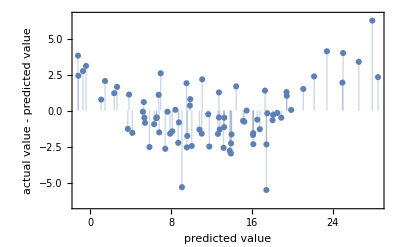

Predictor information
Data type | Mixed (number: 10)
Standard deviation | 2.96 ± 0.68
Method | LinearRegression
Single evaluation time | 1.54 ms/example
Batch evaluation speed | 234. examples/ms
Loss | 2.42 ± 0.12
Model memory | 281. kB
Training examples used | 256 examples
Training time | 1.43 s
 |

```mathematica
pLRv2=Predict[finalTrain,Method->"LinearRegression"]
pmLRv2=PredictorMeasurements[pLRv2,finaltest]
pmLRv2["ComparisonPlot"]
pmLRv2["MeanSquare"]
pmLRv2["ResidualPlot"]
Information[pLRv2]
```

PredictorFunction[…]

PredictorMeasurementsObject[…]

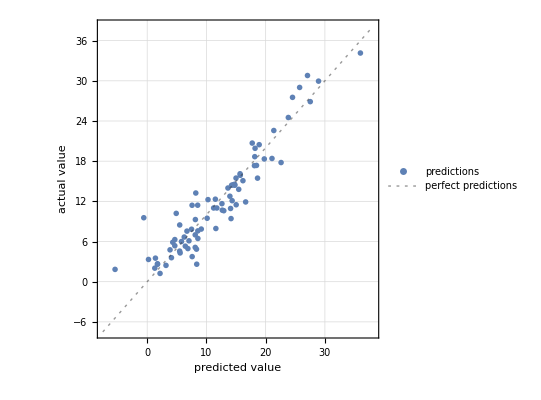

6.99146

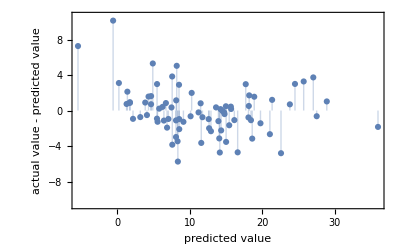

Predictor information
Data type | Mixed (number: 10)
Standard deviation | 3.3 ± 0.62
Method | NeuralNetwork
Single evaluation time | 2.26 ms/example
Batch evaluation speed | 46.9 examples/ms
Loss | 2.57 ± 0.14
Model memory | 246. kB
Training examples used | 256 examples
Training time | 2 4
 |

```mathematica
pNNnoReg= Predict[finalTrain,Method->{"NeuralNetwork", "NetworkDepth"->3,"NetworkType"->"FullyConnected", MaxTrainingRounds->24000}]
pmNNnoReg=PredictorMeasurements[pNNnoReg,finaltest]
pmNNnoReg["ComparisonPlot"]
pmNNnoReg["MeanSquare"]
pmNNnoReg["ResidualPlot"]
Information[pNNnoReg]
```

PredictorFunction[…]

PredictorMeasurementsObject[…]

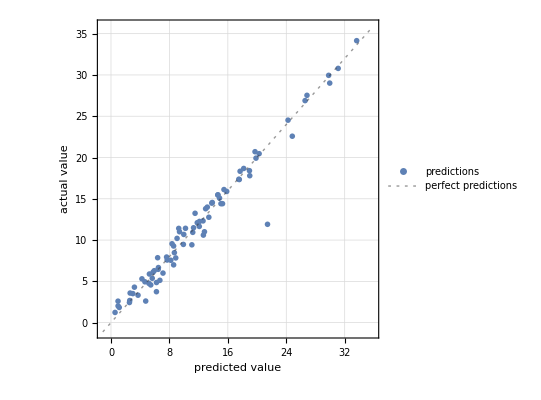

2.07432

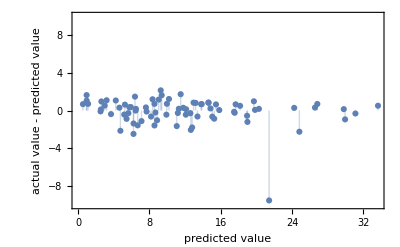

Predictor information
Data type | Mixed (number: 10)
Standard deviation | 2.29 ± 0.87
Method | NeuralNetwork
Single evaluation time | 2.13 ms/example
Batch evaluation speed | 52.9 examples/ms
Loss | 2.08 ± 0.28
Model memory | 226. kB
Training examples used | 256 examples
Training time | 1 55
 |

```mathematica
pNN2layer= Predict[finalTrain,Method->{"NeuralNetwork", "NetworkDepth"->2,"NetworkType"->"FullyConnected","L2Regularization"->0.05, MaxTrainingRounds->24000}]
pmNN2layer=PredictorMeasurements[pNN2layer,finaltest]
pmNN2layer["ComparisonPlot"]
pmNN2layer["MeanSquare"]
pmNN2layer["ResidualPlot"]
Information[pNN2layer]
```

PredictorFunction[…]

PredictorMeasurementsObject[…]

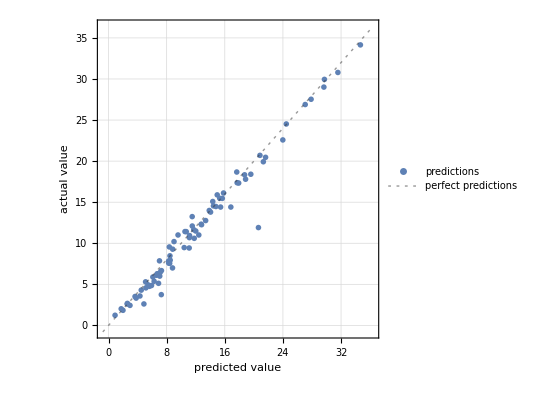

1.83864

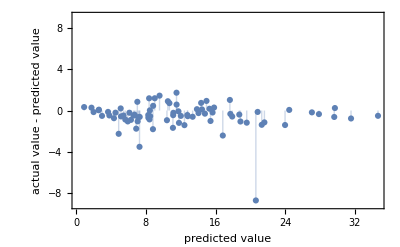

Predictor information
Data type | Mixed (number: 10)
Standard deviation | 2.17 ± 0.92
Method | NeuralNetwork
Single evaluation time | 2.17 ms/example
Batch evaluation speed | 46.9 examples/ms
Loss | 1.88 ± 0.2
Model memory | 260. kB
Training examples used | 256 examples
Training time | 2 9
 |

```mathematica
pNN4layer= Predict[finalTrain,Method->{"NeuralNetwork", "NetworkDepth"->4,"NetworkType"->"FullyConnected","L2Regularization"->0.05, MaxTrainingRounds->24000}]
pmNN4layer=PredictorMeasurements[pNN4layer,finaltest]
pmNN4layer["ComparisonPlot"]
pmNN4layer["MeanSquare"]
pmNN4layer["ResidualPlot"]
Information[pNN4layer]
```

NetChain[<>]

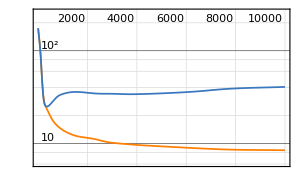
NetTrain Results
summary | ,,  batches:40000  rounds:10000  time:45s  examples/s:57164
data | ,,  training examples:256  validation examples:80  processed examples:2560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64CPU
round | ,,  loss:8.45
validation | ,,  loss:4.07×10^1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set |

```mathematica
netSimple400v2=NetChain[{10,BatchNormalizationLayer[],Tanh,30,30,30,30,BatchNormalizationLayer[],Tanh,1}]
trainedNetSimple400v2=NetTrain[netSimple400v2,finalTrain,All,ValidationSet->finaltest,MaxTrainingRounds->10000,Method->{"ADAM","LearningRate"->0.0005, "L2Regularization"->0.3}]
```

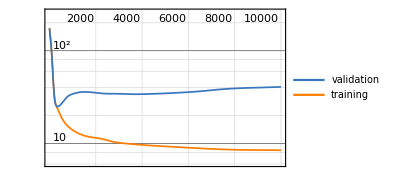
<|Loss→ | rounds
loss | -Graphics-|>

44.7837

<|Loss→8.44841|>

380

25.0069

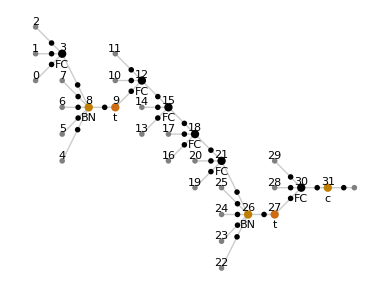

-Graphics-

```mathematica
trainedNetSimple400v2["FinalPlots"]
trainedNetSimple400v2["TotalTrainingTime"]
trainedNetSimple400v2["RoundMeasurements"]
best=trainedNetSimple400v2["BestValidationRound"]
trainedNetSimple400v2["ValidationLossList"][[best]]
NetInformation[trainedNetSimple400v2["TrainedNet"],"MXNetNodeGraphPlot"]
NetInformation[trainedNetSimple400v2["TrainedNet"],"SummaryGraphic"]
```

NetChain[<>]

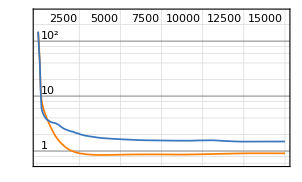
NetTrain Results
summary | ,,  batches:60000  rounds:15000  time:1.2min  examples/s:53811
data | ,,  training examples:256  validation examples:80  processed examples:3840000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64CPU
round | ,,  loss:9.09×10^-1
validation | ,,  loss:1.48
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set |

```mathematica
netSimple400v3=NetChain[{BatchNormalizationLayer[],Tanh,50,50,50,50,50,50,BatchNormalizationLayer[],Tanh,1}]
trainedNetSimple400v3=NetTrain[netSimple400v3,finalTrain,All,ValidationSet->finaltest,MaxTrainingRounds->15000,Method->{"ADAM","LearningRate"->0.0005, "L2Regularization"->0.05}]
```

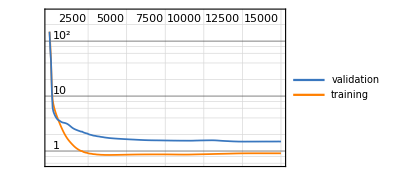
<|Loss→ | rounds
loss | -Graphics-|>

71.3604

<|Loss→0.908735|>

12853

1.46082

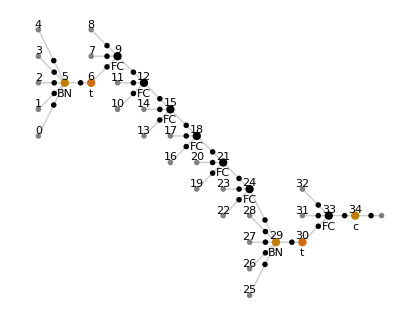

-Graphics-

```mathematica
trainedNetSimple400v3["FinalPlots"]
trainedNetSimple400v3["TotalTrainingTime"]
trainedNetSimple400v3["RoundMeasurements"]
best=trainedNetSimple400v3["BestValidationRound"]
trainedNetSimple400v3["ValidationLossList"][[best]]
NetInformation[trainedNetSimple400v3["TrainedNet"],"MXNetNodeGraphPlot"]
NetInformation[trainedNetSimple400v3["TrainedNet"],"SummaryGraphic"]
```

NetChain[<>]

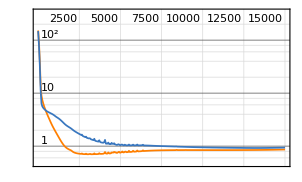
NetTrain Results
summary | ,,  batches:60000  rounds:15000  time:1.2min  examples/s:55549
data | ,,  training examples:256  validation examples:80  processed examples:3840000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64CPU
round | ,,  loss:8.63×10^-1
validation | ,,  loss:9.37×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set |

```mathematica
netSimple400v4=NetChain[{BatchNormalizationLayer[],Tanh,50,50,50,50,50,BatchNormalizationLayer[],Tanh,1}]
trainedNetSimple400v4=NetTrain[netSimple400v4,finalTrain,All,ValidationSet->finaltest,MaxTrainingRounds->15000,Method->{"ADAM","LearningRate"->0.0005, "L2Regularization"->0.05}]
```

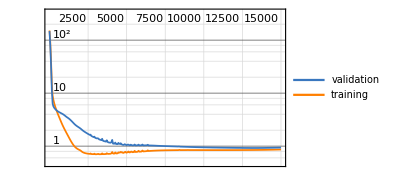
<|Loss→ | rounds
loss | -Graphics-|>

69.128

<|Loss→0.863038|>

13218

0.919938

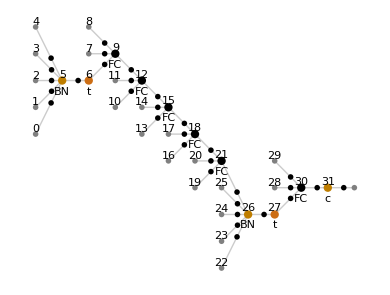

-Graphics-

```mathematica
trainedNetSimple400v4["FinalPlots"]
trainedNetSimple400v4["TotalTrainingTime"]
trainedNetSimple400v4["RoundMeasurements"]
best=trainedNetSimple400v4["BestValidationRound"]
trainedNetSimple400v4["ValidationLossList"][[best]]
NetInformation[trainedNetSimple400v4["TrainedNet"],"MXNetNodeGraphPlot"]
NetInformation[trainedNetSimple400v4["TrainedNet"],"SummaryGraphic"]
```

```mathematica
netSimple400v5=NetChain[{BatchNormalizationLayer[],Tanh,50,50,50,50,50,50,BatchNormalizationLayer[],Tanh,1}]
trainedNetSimple400v5=NetTrain[netSimple400v5,finalTrain,All,ValidationSet->finaltest,MaxTrainingRounds->15000,Method->{"ADAM","LearningRate"->0.0005, "L2Regularization"->0.05}]
```

NetChain[<>]

NetTrain Results
summary | ,,  batches:60000  rounds:15000  time:1.2min  examples/s:54887
data | ,,  training examples:256  validation examples:80  processed examples:3840000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64CPU
round | ,,  loss:9.09×10^-1
validation | ,,  loss:1.48
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set |

```mathematica
trainedNetSimple400v5["FinalPlots"]
trainedNetSimple400v5["TotalTrainingTime"]
trainedNetSimple400v5["RoundMeasurements"]
best=trainedNetSimple400v5["BestValidationRound"]
trainedNetSimple400v5["ValidationLossList"][[best]]
NetInformation[trainedNetSimple400v5["TrainedNet"],"MXNetNodeGraphPlot"]
NetInformation[trainedNetSimple400v5["TrainedNet"],"SummaryGraphic"]
```

<|Loss→ | rounds
loss | -Graphics-|>

69.9616

<|Loss→0.908735|>

12853

1.46082

-Graphics-

-Graphics-

NetChain[<>]

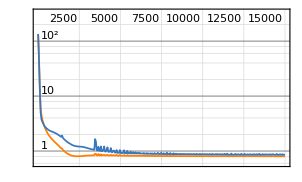
NetTrain Results
summary | ,,  batches:60000  rounds:15000  time:1.3min  examples/s:49423
data | ,,  training examples:256  validation examples:80  processed examples:3840000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64CPU
round | ,,  loss:8.13×10^-1
validation | ,,  loss:9.07×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set |

```mathematica
netSimple400v6=NetChain[{BatchNormalizationLayer[],Tanh,100,100,100,100,100,BatchNormalizationLayer[],Tanh,1}]
trainedNetSimple400v6=NetTrain[netSimple400v6,finalTrain,All,ValidationSet->finaltest,MaxTrainingRounds->15000,Method->{"ADAM","LearningRate"->0.0005, "L2Regularization"->0.05}]
```

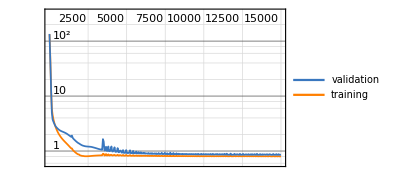
<|Loss→ | rounds
loss | -Graphics-|>

77.6971

<|Loss→0.812835|>

14281

0.827167

-Graphics-

-Graphics-

```mathematica
trainedNetSimple400v6["FinalPlots"]
trainedNetSimple400v6["TotalTrainingTime"]
trainedNetSimple400v6["RoundMeasurements"]
best=trainedNetSimple400v6["BestValidationRound"]
trainedNetSimple400v6["ValidationLossList"][[best]]
NetInformation[trainedNetSimple400v6["TrainedNet"],"MXNetNodeGraphPlot"]
NetInformation[trainedNetSimple400v6["TrainedNet"],"SummaryGraphic"]
```

NetChain[<>]

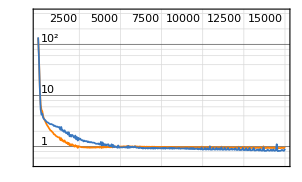
NetTrain Results
summary | ,,  batches:60000  rounds:15000  time:1.5min  examples/s:41845
data | ,,  training examples:256  validation examples:80  processed examples:3840000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64CPU
round | ,,  loss:9.38×10^-1
validation | ,,  loss:8.41×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set |

```mathematica
netSimple400v7=NetChain[{BatchNormalizationLayer[],Tanh,100,100,100,100,100,100,BatchNormalizationLayer[],Tanh,1}]
trainedNetSimple400v7=NetTrain[netSimple400v7,finalTrain,All,ValidationSet->finaltest,MaxTrainingRounds->15000,Method->{"ADAM","LearningRate"->0.0005, "L2Regularization"->0.05}]
```

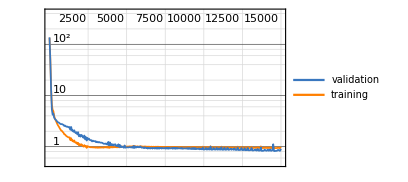
<|Loss→ | rounds
loss | -Graphics-|>

91.7673

<|Loss→0.937657|>

13707

0.760799

-Graphics-

-Graphics-

```mathematica
trainedNetSimple400v7["FinalPlots"]
trainedNetSimple400v7["TotalTrainingTime"]
trainedNetSimple400v7["RoundMeasurements"]
best=trainedNetSimple400v7["BestValidationRound"]
trainedNetSimple400v7["ValidationLossList"][[best]]
NetInformation[trainedNetSimple400v7["TrainedNet"],"MXNetNodeGraphPlot"]
NetInformation[trainedNetSimple400v7["TrainedNet"],"SummaryGraphic"]
```